# Fourierova transformacija

F(ω)=∫_(-∞)^∞ f(t)ⅇ^ⅈωt ⅆt                             Fourierova transformacija

f(t)=1/(2π)∫_(-∞)^∞ F(ω)ⅇ^-ⅈωt ⅆω                 inverzna formula

F_s(ω)=∫_0^∞ f(t)sin(ωt)ⅆt                       sinusna Fourierova transformacija
F_c(ω)=∫_0^∞ f(t)cos(ωt)ⅆt                      kosinusna Fourierova transformacija

Pred prvo nalogo se spomnimo, da so za definicijo zlepljene funkcije primerni ukazi If, Which ali Piecewise .

```mathematica
?If
?Which
?Piecewise
```

1. Narišite graf funkcije
      f(t) = {sin t | ,    če
0 | ,    če 0≤ t ≤ π
t<0  ali  t>π

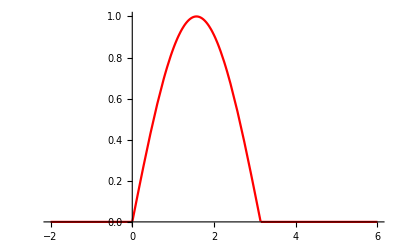

```mathematica
f[t_] :=If[0≤ t<Pi, Sin[t],0]
Plot[f[t], {t,-2,6}, PlotStyle->Red]
```

2. Poiščite Fourierovo transformiranko funkcije iz 1. naloge.
     Nato izračunajte inverzno Fourierovo transformiranko dobljene funkcije in grafično preverite, da se rezultat ujema s prvotno funkcijo.
     Nalogo rešite na dva načina:
     a) Po definiciji transformirank in z ukazom Integrate za določeni integral.
     b) Mathematica ima za integralske transformacije vgrajene ukaze: FourierTransform, ...

(1+ⅇ^(ⅈ π w))/(1-w^2)

(1+ⅇ^(ⅈ π w))/(√(2 π) (1-w^2))

(1+ⅇ^(ⅈ π w))/(1-w^2)

1/2 (1/Sign[π-t]+1/Sign[t]) Sin[t]

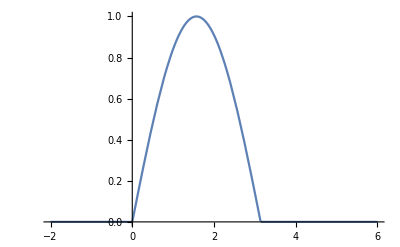

```mathematica
Integrate[f[t]*E^(I w t), {t, - Infinity, Infinity}]
(*esc inf esc*)
FourierTransform[f[t],t,w] 
F= FourierTransform[f[t],t,w, FourierParameters->{1, 1}] (*Parameters damo da popravimo definicijo ki jo uprablje mathematica!!!!*)

(*Definicija f trensformirank je različno *)

ff= InverseFourierTransform[F, w, t, FourierParameters -> {1,1}]
Plot[ff,{t,-2,6}]
```

Razlika med rešitvama je v ne čisto enakih definicijah Fourierove transformiranke in njene inverzne funkcije.
Tu so tri različne konvencije, ki jih razni avtorji uporabljajo:

          F(ω)=∫_(-∞)^∞ f(t)ⅇ^ⅈωt ⅆt                          f(t)=1/(2π)∫_(-∞)^∞ F(ω)ⅇ^-ⅈtω ⅆω                (Tomšič,Slivnik)
F(ω)=1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^ⅈωt ⅆt               f(t)=1/(√(2π))∫_(-∞)^∞ F(ω)ⅇ^-ⅈtω ⅆω           (Wolfram Mathematica)
F(ω)=1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^-ⅈωt ⅆt            f(t)=1/(√(2π))∫_(-∞)^∞ F(ω)ⅇ^ⅈtω ⅆω              (Kreyszig)

Program Mathematica se tem konvencijam prilagaja z opcijo FourierParameters.
Mi torej uporabljamo FourierParameters->{1,1}.

Pred naslednjo nalogo spoznajmo ukaz Manipulate, ki ga uporabljamo za dinamično predstavitev raznih rezultatov.

```mathematica
Manipulate[
Plot[a(x-b)^2+c,{x,-5,5},PlotRange->{-20,20},PlotStyle->Thick],
{a,-3,3},{b,-3,3},{c,-3,3}]
```

3. Uporabite ukaz Manipulate in prikažite grafa funkcije f(t)=e^(-t^2/a) in njene Fourierove transformiranke v isti koordinatni sistem za vrednosti parametra a∈[1,5]. NUJNO ; DA PORAČUNE IN NE IZRIŠE.

```mathematica
Manipulate[
f=E^(-t^2/a);
F = FourierTransform[f,t,w, FourierParameters->{1,1}];
Graff=Plot[f, {t,-5,5}];
Graft = Plot[F, {w,-5,5},PlotStyle-> Red];
Show[Graff, Graft, PlotRange-> {0,5}], {a, 1,5}]
```

4. Z ukazom Plot narišite graf funkcije
     f(t) = {e^(-t/7)sin(10t) | ,    če
0 | ,    če     t ≥0
t<0 
in narišite graf gostote spektra |F(ω)| z ukazom LogLogPlot na intervalu ω∈[0.1 , 100]! (dvojna logaritemska skala na x in y) To je frekvenčna slika. Pri eni frekvenci imamo eak. To je veliko bolj zastopana vrednost. Pri 10.

Piecewise[{{ⅇ^(-t/7) Sin[10 t], t≥0}, {0, True}}]

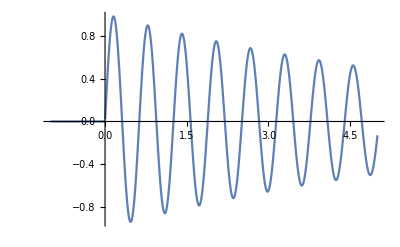

-490/(-4901+14 ⅈ w+49 w^2)

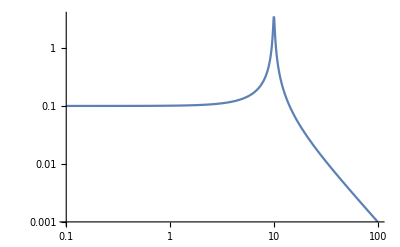

```mathematica
Clear[f,F,t,w]
f= Piecewise[{{E^(-t/7)* Sin[10 t], t≥ 0},{0, t<0}}]
Plot[f,{t,-1,5}]
F = FourierTransform[f,t,w, FourierParameters->{1, 1}]
LogLogPlot[Abs[F], {w,0.1, 100}]
```

### Primeri nalog za preverjanje - tipi nalog

6. Poiščite Fourierovo transformiranko F(ω) funkcije f(t)= ⅇ^(-|t|).
     Koliko je F(4)?
  
Rezultat: 0.117647

```mathematica
f = E^-Abs[t]
F= FourierTransform[f,t,w, FourierParameters->{1,1}]/. w-> 4 //N
```

ⅇ^(-Abs[t])

0.117647

7. Funkcija θ(t) je enotna stopnica. V Mathematici se imenuje UnitStep.
     Definirajmo dve funkciji
     f(t) =θ(t-3)-θ(t-5),
     g(t) =(1- |t|) (θ(t-1)-θ(t+1)) .
     Koliko je vrednost konvolucije h(t)=(f*g)(t) v času t = 4.5?
   
Rezultat: -0.875

Piecewise[{{-1/2, t==3}, {1/2 (-4+4 t-t^2), 2<t<3}, {1/2 (-36+12 t-t^2), 5≤t<6}, {1/2 (14-8 t+t^2), 3<t<5}, {0, True}}]

-0.875

-0.875

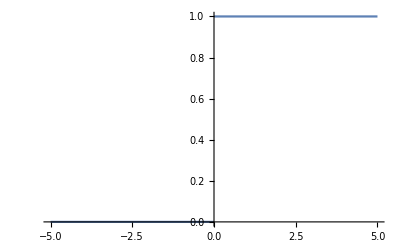

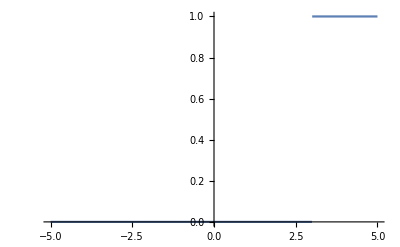

```mathematica
Clear[f,g,t]
f[t_]:= UnitStep[t-3]-UnitStep[t-5]
g[t_]:= (1-Abs[t])(UnitStep[t-1]-UnitStep[t+1])
konv= Integrate[f[t-u]*g[u], {u,-∞, ∞}]
konv/. t-> 4.5

(*ali z konvolve - pazi convolve lahko uporabimo samo za fourierjevo*)
Convolve [f[u],g [u],u,t]/. t-> 4.5

Plot[UnitStep[t],{t,-5,5}]
Plot[UnitStep[t-3],{t,-5,5}]
```

8. Poiščite inverzno Fourierovo transformiranko funkcije F(ω) = ⅇ^(-2|ω|).
     Koliko je f(1/2)?

Rezultat: 0.149793

```mathematica
F= E^(-2Abs[w])
InverseFourierTransform[F, w, t, FourierParameters->{1,1}]/. t-> 0.5
```

ⅇ^(-2 Abs[w])

0.149793

9. Poiščite kosinusno Fourierovo transformiranko F_c(ω) funkcije f(t)=θ(t-2) - θ(t-6).
      Nato poiščite ničle funkcije F_c(ω). Koliko je najmanjša pozitivna ničla?

Rezultat: 0.392699

-UnitStep[-6+t]+UnitStep[-2+t]

(2 (-Sin[2 w]+Sin[6 w]))/w

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-1.5708,1.5708,-1.9635,1.9635,-1.1781,1.1781,-2.74889,2.74889,-0.392699,0.392699}

0.392699

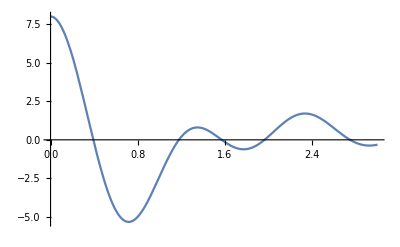

```mathematica
f= UnitStep[t-2]- UnitStep[t-6]
kos= FourierCosTransform[f, t, w, FourierParameters->{1, 1}]
w/.Solve[kos== 0, w]//N
0.3926990816987242 
Plot[kos, {w,0,3}]
```

### Analiza konvolucije funkcije f(t) s “konstanto”

Naloga je odkriti, kakšno preoblikovanje poljubne funkcije f(t) predstavlja konvolucija te funkcije z naslednjo "konstantno" funkcijo. 
konst (t) = {1/(2σ) | , če | t |≤ σ
    0      | , če | t |> σ
Kakšen je vpliv parametra σ?

Izpeljemo:
(f*konst)(t)= ∫_(-∞)^∞ f(u)konst(t-u)ⅆu = 1/(2σ)∫_(t-σ)^(t+σ) f(u)ⅆu=
1/(2σ)*( ploščina pod krivuljo f(u) na intervalu t-σ<u<t+σ )=
povprečna vrednost funkcije f(u) na tem intervalu

Which[t<-σ,0,t<σ,1/(2 σ),True,0]

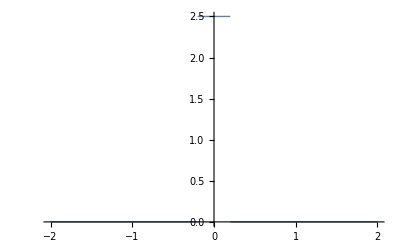

```mathematica
konst[t_,σ_]=Which[t<-σ,0,t<σ,1/(2σ),True,0]
Plot[konst[t,0.2],{t,-2,2},PlotStyle->Thick]
(*kvluc[t_,σ_]=Integrate[f[u]konst[t-u,σ],{u,-∞,∞}];*)
kvluc[t_,σ_]:=1/(2σ)Integrate[f[u],{u,t-σ,t+σ}];
```

Za primer vzemimo naslednjo nezvezno funkcijo f(t).

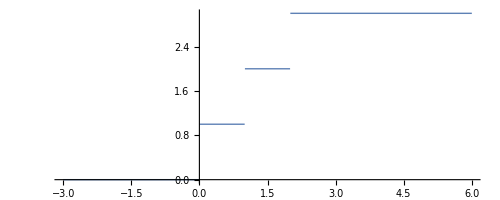

```mathematica
Clear[f]
f[t_]=Which[t<0,0,t<1,1,t<2,2,True,3];
graff=Plot[f[t],{t,-3,6},PlotStyle->Thick,AspectRatio->Automatic]

(* formula za ploščino pod f[t] v širini 2σ okrog t *)
plosc[t_,σ_]:=Block[{ogli,n},
ogli={{t+σ,f[t+σ]},{t+σ,0},{t-σ,0},{t-σ,f[t-σ]}};
For[n=Max[Ceiling[t-σ],0],n≤Min[Floor[t+σ],3],n++,
ogli=Join[ogli,{{n,n},{n,f[n]}}];]
(*Print[ogli]*);
Polygon[ogli]
]
```

V naslednjem ukazu Manipulate:
Z miško vlečemo neodvisno spremenljivko t po abscisni osi.
Rdeča pika sledi vrednosti konvolucije (f*konst)(t).
Zeleno je obarvana ploščina pod funkcijo f(t) na intervalu (t-σ, t+σ).
Parameter σ lahko spreminjamo.

```mathematica
Manipulate[
Show[
graff,(* graf funkcije *)
Graphics[
{FontSize->18,
Text["t",{tt_⟦1⟧,-0.4}],
Text[StringJoin["σ= ",ToString[σ]],{-2.5,2.5}],
{RGBColor[0.8,1,0.8],plosc[tt_⟦1⟧,σ]}, (* zelena plosčina *){RGBColor[1,0,0],Disk[{tt_⟦1⟧,kvluc[tt_⟦1⟧,σ]},0.1]}} (* rdeča pika *)
],PlotRange->{{-3,6},{-0.5,3.5}},AspectRatio->Automatic,ImageSize->{800,300},TicksStyle->Directive[14],Ticks->{{-2,-1,1,2,3,4,5},{1,2,3}}],
{σ,0.1,1},{{tt,{-1,-0.2}},{-1,-0.5},{4,0},Locator,Appearance->None}]
```

V naslednjem ukazu sta prikazana grafa osnovne funkcije in njene konvolucije s “konstanto”.
Opazujmo vpliv parametra σ!

```mathematica
Manipulate[
Show[
graff,
Plot[kvluc[t,σ],{t,-3,6},PlotStyle->{Red,Thick},AspectRatio->Automatic]
],{σ,0.01,1}]
```

Odgovor :
Konvolucija neke funkcije f(t) z dano “konstantno” funkcijo predstavlja glajenje funkcije.
(f*konst)(t) je zvezna funkcija in se prilega funkciji f(t). Parameter σ pomeni stopnjo glajenja.

#### Konvolucija dane funkcije f(t) s "konstanto" oziroma Gaussovo krivuljo 1/(σ √(2π))ⅇ^(-t^2/(2 σ^2))

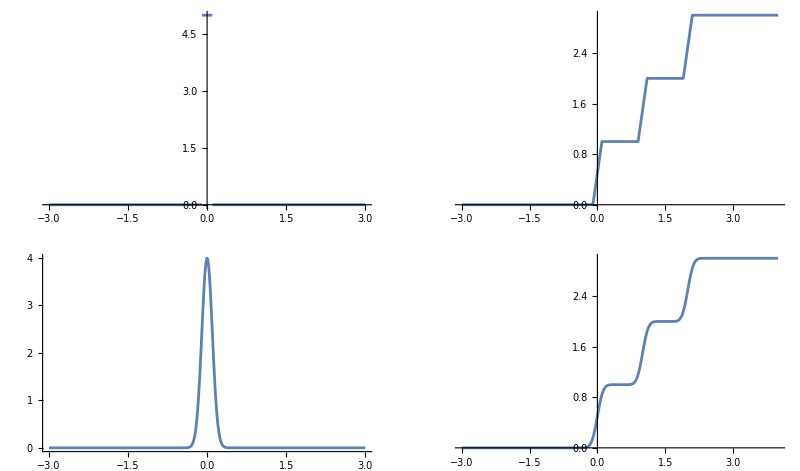

```mathematica
Clear[f]
σ=0.1;
f[t_]:=Which[t<0,0,t<1,1,t<2,2,True,3];
Konst[t_]:=Which[t<-σ,0,t<σ,1/(2σ),True,0];
Gauss[t_]:=Exp[-t^2/(2σ^2)]/(σ Sqrt[2Pi]);

KvlucKonst[t_]:=NIntegrate[Konst[u]f[t-u],{u,-5σ,5σ},AccuracyGoal->4,PrecisionGoal->4];
KvlucGauss[t_]:=NIntegrate[Gauss[u]f[t-u],{u,-5σ,5σ},AccuracyGoal->4,PrecisionGoal->4];

Show[GraphicsGrid[{
{Plot[Konst[t],{t,-3,3},PlotStyle->AbsoluteThickness[2],AspectRatio->Automatic,
TicksStyle->Directive[14],PlotRange->All],
Plot[KvlucKonst[t],{t,-3,4},PlotStyle->AbsoluteThickness[2],AspectRatio->Automatic,TicksStyle->Directive[14]]},
{Plot[Gauss[t],{t,-3,3},PlotStyle->AbsoluteThickness[2],AspectRatio->Automatic,TicksStyle->Directive[14],PlotRange->All],
Plot[KvlucGauss[t],{t,-3,4},PlotStyle->AbsoluteThickness[2],AspectRatio->Automatic,TicksStyle->Directive[14]]}
}]]
```